# Математическое моделирование и сложные процессы.

## Лабораторная работа №1 Моделирование поведения толпы методом конечных автоматов.

Лицкевич В.Л.

# Задание

Задача: Задан тоннель. Ширина 21 клетка на входе и 7 клеток на выходе. В тоннель прибывают люди со скоростью 11 чел за такт. Каждый человек стремится к выходу из тоннеля. Каждый человек видит ситуацию на 3 клетки в каждую сторону.
Весовые коэффициенты предпочтения движения в данном направлении определяются в зависимотсти от колличества свободных клеток ({0} | {1} | {2} | {3}
0. | 0.5 | 0.75 | 1.), и в зависимости от выгодности направления движения по следующим формулам:

```mathematica
(*Тенденция движения:{N,E,S,W} d-дирекционный синус:N=(d^2+1/3)/If[d<0,1,3,1];
E=1-d^2;
S=(d^2+1/3)/If[d>0,1,3,1];
W=((d^2+1/3))/6;*)
```

Решение о передвижении в направлениях {N,E,S,W} принимается случайным образом,на основе препочтений каждого участника численного эксперимента.

Задание 1. Построить симуляционную модель, провести возможные оптимизации. Сделать анимацию процесса продолжительностью в 100 тактов.

Задание 2. Запрограммировать численный эксперимент длинной в 1000 тактов. Построить графики колличества вошедших и вышедших за такт. (Ширина сужения 7 клеток)

Задание 3. Провести численный эксперимент для всех сужений от 0 до 15 клеток шириной, и выяснить оптимальную ширину сужения тоннеля относительно предотвращения образования пробок.

```mathematica
Tunnel[length_,constriction_]:=Module[{InW=21, OutW=7,T,TrT,i,P1,P2,,Q1,Q2,n,line1,line2,k=0,m=0},
T=Table[0,{i,1,InW},{j,1,length}];
T⟦1⟧=T⟦-1⟧=Table[1,{i,1,length}];
TrT=Transpose@T;
TrT⟦1⟧=Table[1,{i,1,InW}];
n=Round[length/8];
For[i=1,i≤n,TrT⟦-i,1;;OutW⟧=TrT⟦-i,InW-OutW+1;;InW⟧=1;i++];
P1={length-n,7};
P2={length-n-constriction-1,1};
Q1={length-n,15};
Q2={length-n-constriction-1,21};
line1[x_,y_]:=(P1⟦2⟧-P2⟦2⟧)x+(P2⟦1⟧-P1⟦1⟧)y+(P1⟦1⟧P2⟦2⟧-P2⟦1⟧P1⟦2⟧);
line2[x_,y_]:=(Q1⟦2⟧-Q2⟦2⟧)x+(Q2⟦1⟧-Q1⟦1⟧)y+(Q1⟦1⟧Q2⟦2⟧-Q2⟦1⟧Q1⟦2⟧);
For[i=1,i≤constriction,While[line1[length-n-i,7-k]<0,k++];
TrT⟦-n-i,;;7-k⟧=1;
i++
];
For[i=1,i≤constriction,While[line2[length-n-i,15+m]>0,m++];
TrT⟦-n-i,15+m;;⟧=1;
i++
];
Transpose@TrT]
DisplayTunnel[Tunnel_]:=Graphics[Table[Which[Tunnel⟦j,i⟧==0,{EdgeForm[Thick],White,Rectangle[{i,22-j}]}, Tunnel⟦j,i⟧==1,{EdgeForm[Thick],Orange,Rectangle[{i,22-j}]}, Tunnel⟦j,i⟧==2,{EdgeForm[Thick],Red,Rectangle[{i,22-j}]}],{i,1,Length@Tunnel⟦1⟧}, {j,1,Length@Tunnel}]]
```

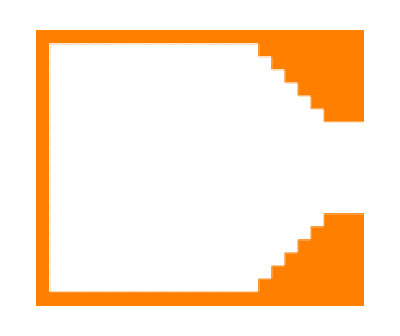

```mathematica
T=Tunnel[25,5];
DisplayTunnel[T]
```

```mathematica
CheckWay[Tunnel_,{i_,j_},way_]:=Module[{w,n},
Which[
way=="N",
w=Quiet@Table[Check[Tunnel⟦i-k,j⟧,1],{k,1,3}],
way=="E",
w=Quiet@Table[Check[Tunnel⟦i,j+k⟧,1],{k,1,3}],
way=="S",
w=Quiet@Table[Check[Tunnel⟦i+k,j⟧,1],{k,1,3}],
way=="W",
w=Quiet@Table[Check[Tunnel⟦i,j-k⟧,1],{k,1,3}]
];
Which[
w⟦1⟧≠0,
	w⟦2⟧=1;
	w⟦3⟧=1,
w⟦2⟧≠0,
	w⟦3⟧=1
];
Which[
j==Dimensions[Tunnel]⟦2⟧-1&&way=="E",
	If[
	w⟦1⟧==0,
		w⟦2⟧=0;
		w⟦3⟧=0
		],
j==Dimensions[Tunnel]⟦2⟧-2&&way=="E",
	If[
	w⟦1⟧==0&&w⟦2⟧==0,
		w⟦3⟧=0
	];
	];
n=Length@Select[w,#==0&];
Which[
n==3,1,
n==2,0.75,
n==1,0.5,
n==0,0]
]
```

```mathematica
Move[Tunnel_,{i_,j_}]:=Module[{d,Nn,Ee,Ss,Ww,NN,EE,SS,WW,NESW, Step="",T=Tunnel},
d = Sin@VectorAngle[{Dimensions[T]⟦2⟧,i}-{1,i},{Dimensions[T]⟦2⟧,11}-{j,i}];
d=If[j<11,d,-d];
Nn=(d^2+1/3)/If[d<0,1,3,1];
Ee=1-d^2;
Ss=(d^2+1/3)/If[d>0,1,3,1];
Ww=((d^2+1/3))/6;

NN=CheckWay[T,{i,j},"N"];
EE=CheckWay[T,{i,j},"E"];
SS=CheckWay[T,{i,j},"S"];
WW=CheckWay[T,{i,j},"W"];

NESW={Nn NN,Ee EE, Ss SS, Ww WW};

Which[
j≠Dimensions[T]⟦2⟧,
	If[NESW≠{0,0,0,0},
	Step = RandomChoice[NESW->{"N","E","S","W"}];
	Which[
	Step=="N",
		T⟦i,j⟧=0;
		T⟦i-1,j⟧=2,
	Step=="E",
		T⟦i,j⟧=0;
		T⟦i,j+1⟧=2,
	Step=="S",
		T⟦i,j⟧=0;
		T⟦i+1,j⟧=2,
	Step=="W",
		T⟦i,j⟧=0;
		T⟦i,j-1⟧=2
	]
	],
j==Dimensions[T]⟦2⟧,
	T⟦i,j⟧=0;
	Step="Ex"
 ];
{T,Step}
]
```

```mathematica
MoveColum[Tunnel_,colum_,yetMoved_:{}]:=Module[{T=Tunnel,CarsInColum,car,AllCars,i,Step,Backed={},Moved=0},
CarsInColum=DeleteCases[Table[If[T⟦i,colum⟧==2,{i,colum}],{i,2,20}],Null];
AllCars=DeleteCases[Flatten[Table[If[T⟦i,j⟧==2,{i,j}],{i,2,20},{j,2,Dimensions[T]⟦2⟧}],1],Null];
For[i=1,i≤Length@yetMoved,
CarsInColum=DeleteCases[CarsInColum,yetMoved⟦i⟧]; i++];
While[Length@CarsInColum≠0,
car = RandomChoice[CarsInColum];
{T,Step}=Move[T,car];
If[Step≠"",Moved++];
If[Step=="W",AppendTo[Backed,car-{0,1}]];
AllCars=DeleteCases[AllCars,car];
CarsInColum=DeleteCases[CarsInColum,car]
];
{T,Backed,Moved}
]
```

```mathematica
MoveTunnel[Tunnel_]:=Module[{i,exit,T=Tunnel,Backed={},AllCars,Moved,M=0,Proc},
AllCars=Length@DeleteCases[Flatten[Table[If[T⟦i,j⟧==2,{i,j}],{i,2,20},{j,2,Dimensions[T]⟦2⟧}],1],Null];
exit = Length@Select[T⟦2;;20,Dimensions[T]⟦2⟧⟧,#==2&];
For[i=Dimensions[T]⟦2⟧,i>1,
{T,Backed,Moved}=MoveColum[T,i,Backed];
M+=Moved;
i--];
Proc=Quiet[Check[M/AllCars//N,0]];
{T,exit,Proc}]
```

```mathematica
Arr[{Tunnel_,exit_,p_}]:=Module[{F, T=Tunnel,Em,New,i,arr},
F= T⟦;;,2⟧;
Em=DeleteCases[Table[If[F⟦i⟧==0,i],{i,1,Length@F}],Null];
New = If[Length@Em≥11,RandomSample[Em,11],Em];
For[i=1,i≤Length@New,
	T⟦New⟦i⟧,2⟧=2;
	i++];
arr=Length@New;
{T,arr,exit,p}
]
```

```mathematica
T=Tunnel[25,5];
```

```mathematica
G=Table[{T,arr,exit,p}=Arr[MoveTunnel[T]],{i,1,100}];
Tt=Table[DisplayTunnel[G⟦i⟧⟦1⟧],{i,1,100}];
ARR=Table[G⟦i⟧⟦2⟧,{i,1,100}];
EXIT=Table[G⟦i⟧⟦3⟧,{i,1,100}];
P=Table[G⟦i⟧⟦4⟧,{i,1,100}];
```

```mathematica
ListAnimate[Table[Tt⟦i⟧,{i,1,100}]]
```

```mathematica
T=Tunnel[35,15];
G=Table[{T,arr,exit,p}=Arr[MoveTunnel[T]],{i,1,1000}];
Tt=Table[DisplayTunnel[G⟦i⟧⟦1⟧],{i,1,1000}];
ARR=Table[G⟦i⟧⟦2⟧,{i,1,1000}];
EXIT=Table[G⟦i⟧⟦3⟧,{i,1,1000}];
P=Table[G⟦i⟧⟦4⟧,{i,1,1000}];
Mean@P
ListAnimate[Table[Tt⟦i⟧,{i,1,1000}]]
```

0.424686

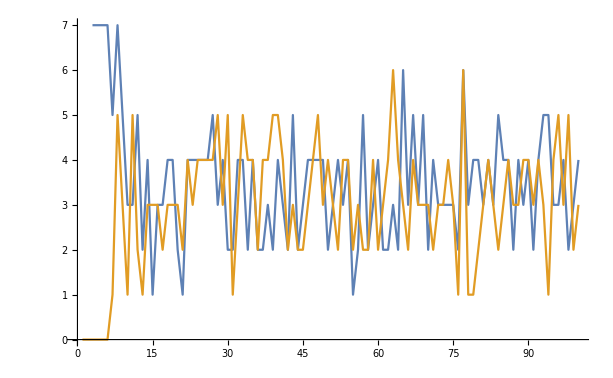

```mathematica
ListLinePlot[{Table[ARR⟦i⟧,{i,1,Length@ARR,10}],Table[EXIT⟦i⟧,{i,1,Length@EXIT,10}]}]
```

```mathematica
Table[T=Tunnel[35,i];G=Table[{T,arr,exit,p}=Arr[MoveTunnel[T]],{i,1,100}];P=Mean@Table[G⟦i⟧⟦4⟧,{i,1,100}],{i,0,15}]
```

{0.728419,0.73186,0.704903,0.728503,0.714508,0.698333,0.704215,0.69955,0.69998,0.70252,0.693256,0.684452,0.693398,0.684378,0.674425,0.685875}